## PHAS2443 2014 exam Hayk Khachatryan

## Question 1

```mathematica
Select[Range[2,2000], PrimeQ]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541,547,557,563,569,571,577,587,593,599,601,607,613,617,619,631,641,643,647,653,659,661,673,677,683,691,701,709,719,727,733,739,743,751,757,761,769,773,787,797,809,811,821,823,827,829,839,853,857,859,863,877,881,883,887,907,911,919,929,937,941,947,953,967,971,977,983,991,997,1009,1013,1019,1021,1031,1033,1039,1049,1051,1061,1063,1069,1087,1091,1093,1097,1103,1109,1117,1123,1129,1151,1153,1163,1171,1181,1187,1193,1201,1213,1217,1223,1229,1231,1237,1249,1259,1277,1279,1283,1289,1291,1297,1301,1303,1307,1319,1321,1327,1361,1367,1373,1381,1399,1409,1423,1427,1429,1433,1439,1447,1451,1453,1459,1471,1481,1483,1487,1489,1493,1499,1511,1523,1531,1543,1549,1553,1559,1567,1571,1579,1583,1597,1601,1607,1609,1613,1619,1621,1627,1637,1657,1663,1667,1669,1693,1697,1699,1709,1721,1723,1733,1741,1747,1753,1759,1777,1783,1787,1789,1801,1811,1823,1831,1847,1861,1867,1871,1873,1877,1879,1889,1901,1907,1913,1931,1933,1949,1951,1973,1979,1987,1993,1997,1999}

## Question 2

```mathematica
r = √(x^2+y^2+z^2)
ψ = z/r

r = {x,y,z}
p = -ⅈ ℏ{δ/δx ,δ/δy,δ/δz}

L = r ×p

L[[3]] ψ
```

√(x^2+y^2+z^2)

z/(√(x^2+y^2+z^2))

{x,y,z}

{-(ⅈ δ ℏ)/δx,-(ⅈ δ ℏ)/δy,-(ⅈ δ ℏ)/δz}

{(ⅈ z δ ℏ)/δy-(ⅈ y δ ℏ)/δz,-(ⅈ z δ ℏ)/δx+(ⅈ x δ ℏ)/δz,(ⅈ y δ ℏ)/δx-(ⅈ x δ ℏ)/δy}

(z ((ⅈ y δ ℏ)/δx-(ⅈ x δ ℏ)/δy))/(√(x^2+y^2+z^2))

```mathematica
ϕ = (L[[1]] +ⅈ L[[2]])ψ
```

(z ((ⅈ z δ ℏ)/δy-(ⅈ y δ ℏ)/δz+ⅈ (-(ⅈ z δ ℏ)/δx+(ⅈ x δ ℏ)/δz)))/(√(x^2+y^2+z^2))

```mathematica
L[[3]] ϕ
```

(z ((ⅈ y δ ℏ)/δx-(ⅈ x δ ℏ)/δy) ((ⅈ z δ ℏ)/δy-(ⅈ y δ ℏ)/δz+ⅈ (-(ⅈ z δ ℏ)/δx+(ⅈ x δ ℏ)/δz)))/(√(x^2+y^2+z^2))

## Question 3

```mathematica
Clear[ψ, schro, V]

schro = {-1/2 D[ψ[x,t], x,x]+V[x]ψ[x,t] == ⅈ D[ψ[x,t], t]}
ψ[x_,0] := ⅇ^((ⅈ π x)/5)ⅇ^(-(x+5)^2)

bc = {ψ[-10,t]  == ψ[-10, 0], ψ[5,t] == ψ[5,0]}

V[x_] := 10 ⅇ^(-x^2)
```

{V[x] ψ[x,t]-1/2 ψ^(2,0)[x,t]==ⅈ ψ^(0,1)[x,t]}

{ψ[-10,t]==1/ⅇ^25,ψ[5,t]==-1/ⅇ^100}

```mathematica
nSol =
NDSolve[
Join[schro,bc],
ψ,
{x, -10, 5},
{t, 0, 2.5}]
```

NDSolve::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

{{ψ→InterpolatingFunction[{{-10., 5.}, {0., 2.5}}, <>]}}

```mathematica
Plot3D[
Re[ψ[x,t] /. nSol],
{x, -10, 5},
{t, 0, 2.5},
ViewPoint -> {0,Infinity, 0}
]
```

-Graphics3D-

## Question 4

```mathematica
p =Plot3D[
LaguerreL[3, √(x^2+y^2)],
{x, -3, 3},
{y, -3,3}]
```

-Graphics3D-

```mathematica
pp = ParametricPlot3D[{Cos[u], Sin[u], 0}, {u, 0, 2π}]
```

-Graphics3D-

```mathematica
Show[p, pp]
```

-Graphics3D-

## Question 5

{x[t]+6 x'[t]+x''[t]==1/2 Sin[3 t]}

{x[0]==3,x'[0]==0}

{{x→InterpolatingFunction[{{0., 30.}}, <>]}}

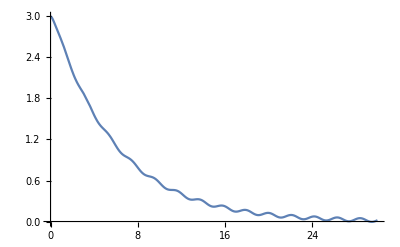

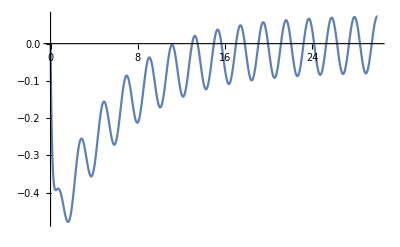

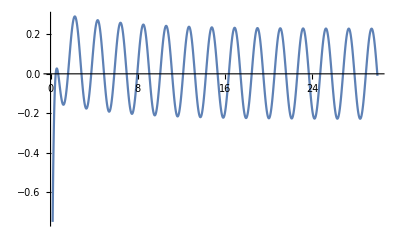

```mathematica
Clear[eq,bc, sol] 

eq = {x''[t] + 6x'[t] + x[t] == 1/2 Sin[3t]}
bc ={x[0] == 3, x'[0] == 0}

sol = 
NDSolve[
Join[eq, bc],
x,
{t, 0, 30}]

Plot[x[t] /. sol, {t, 0, 30}]
Plot[x'[t] /. sol, {t, 0, 30}]
Plot[x''[t] /. sol, {t, 0, 30}]
```

## Question 6

```mathematica
Clear[c]

c[n_] := 
(2n+1)/2 Integrate[LegendreP[n, x] (Cos[x] +3 ⅇ^(-x^2)), {x, -1,1}]
```

```mathematica
c[2]
```

5/2 (-9/(2 ⅇ)+6 Cos[1]+3/4 √π Erf[1]-4 Sin[1])

```mathematica
Clear[function]

function[n_] :=
Sum[
LegendreP[i,x] c[i],
{i, 0, n}]
```

```mathematica
ff[y_,n_] := function[n] //. x-> y
```

```mathematica
Plot[ff[x,5], {x, -1,1}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {-0.999959,-1,1}.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

NIntegrate::itraw: Raw object -0.999959 cannot be used as an iterator.

General::stop: Further output of NIntegrate::itraw will be suppressed during this calculation.

-Graphics-

## Question 7

```mathematica
Clear[T, S, Δt, sho, function]

sho = (q B)/m
T :=sho Δt/2

S := 2 T/(1+Abs[T]^2)


function[{{x1_,x2_,x3_},{v1_,v2_,v3_}}]:=
Module[
{xP, vP, xPP, vPP},

xP = {x1, x2, x3} + Δt/2{v1,v2,v2};
vP = {v1, v2, v3} + {v1,v2,v3} × T;

vPP = {v1,v2,v3} + vP × S;

xPP = xP + Δt/2 vPP;
{xPP, vPP}]
```

(B q)/m

```mathematica
Δt = 0.1

sho = {0,0,1}
l =NestList[function, {{0,1,0}, {10,0,0.5}}, 1000]
```

0.1

{0,0,1}

{{{0,1,0},{10,0,0.5}},{{0.997506,0.950125,0.025},{9.95012,-0.997506,0.5}},{{1.98506,0.800996,0.000124688},{9.801,-1.98506,0.5}},996,{{-6.5493,-1.44311,23.5897},{7.55689,6.5493,0.5}},{{-5.76283,-0.8275,23.9422},{8.1725,5.76283,0.5}}}
 |  |  |  |

```mathematica
ListPlot3D[Transpose[l][[1]]]
```

-Graphics3D-

```mathematica
Transpose[l][[2]][[
```

{10,0,0.5}

```mathematica
K = Norm[#]^2& /@ Transpose[l][[2]]
```

{100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25,100.25}

## Question 8

```mathematica
U1 = Table[RandomReal[], 10000]
U2 = Table[RandomReal[], 10000]
```

{0.709966,0.999917,0.683061,0.622323,0.490062,0.353635,9988,0.882782,0.990229,0.182068,0.996481,0.261754,0.817113}
 |  |  |  |

{0.356282,0.567088,0.591456,0.889295,0.863672,0.385521,9988,0.506665,0.985675,0.758229,0.46729,0.436258,0.863872}
 |  |  |  |

```mathematica
z0 = 3(Sqrt[-2 Log[U1]] Cos[2π U2])+1
z1 = 3(Sqrt[-2Log[U1]]Sin[2π U2])+1
```

{-0.537656,0.964727,-1.19867,3.24307,3.34699,-2.25402,9988,-0.496749,1.4187,1.28616,0.753406,-3.52316,2.25077}
 |  |  |  |

{2.94969,0.984183,-0.423701,-0.872425,-1.70734,3.84994,9988,0.937282,0.962212,-4.52982,1.05141,2.91503,-0.439159}
 |  |  |  |

```mathematica
Mean[z00]
StandardDeviation[z00]

Mean[z11]
StandardDeviation[z11]
```

0.973104

2.94908

0.971679

2.97222

```mathematica
z00=Select[z0, -9<# < 9 &]
z11 = Select[z1, -9 < # < 9 &]
```

{-0.537656,0.964727,-1.19867,3.24307,3.34699,-2.25402,9941,-0.496749,1.4187,1.28616,0.753406,-3.52316,2.25077}
 |  |  |  |

{2.94969,0.984183,-0.423701,-0.872425,-1.70734,3.84994,9935,0.937282,0.962212,-4.52982,1.05141,2.91503,-0.439159}
 |  |  |  |

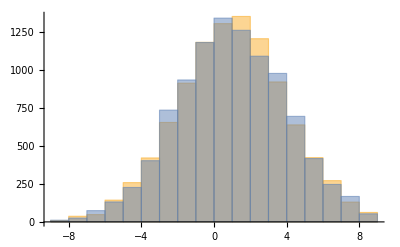

```mathematica
Histogram[{z00, z11}]
```

```mathematica
StandardDeviation[3z0]
```

3.00876